```mathematica
d=-0.12; t=0.4; c=6.25;a1=0.00125; G1=0.00086; b=0.00003138; 
f4[x_,n1_,U_]:=√(d^2+U^2+(a1*n1/x)+t^2/2-√((t^2+4*U^2)*(a1*n1/x)+4*U^2*d^2+2*t^2*d*U+t^4/4));
f6[x_,n1_,U_]:=√(d^2+U^2+(a1*n1/x)+t^2-2*√((t^2+U^2)*(a1*n1/x)+U^2*d^2));
f4[0.1,1,0.1];
Plot[{f4[x,1,0.10],f4[x,2,0.10],f4[x,3,0.10],f4[x,1,0.14],f4[x,2,0.14],f4[x,3,0.14],0.225},{x,0,0.5},PlotRange->{0.180,0.32},PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Red},{Thickness[0.003],Red},{Thickness[0.003],Green},{Thickness[0.003],Green},{Thickness[0.003],Green},{Thickness[0.003],Dashed,Black},{Thickness[0.003],Dashed,Black}},Epilog->{{Black,Text["U = 100  meV",{0.36,0.304},{-1,-1}]},{Black,Text["U = 140 meV",{0.36,0.292},{-1,-1}]}},FrameLabel->{Style["1/B, T^-1",10],Style["E, eV",10]},Frame->True]
```

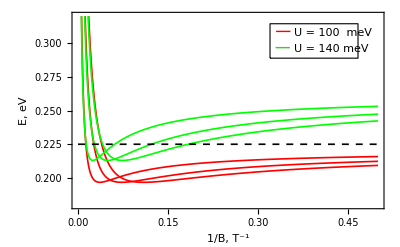

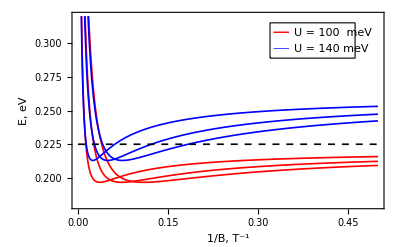

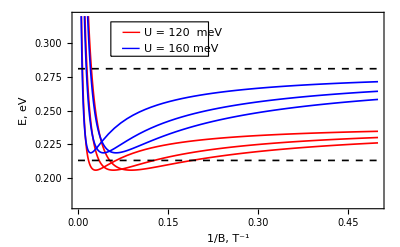

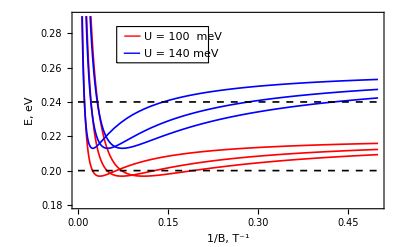

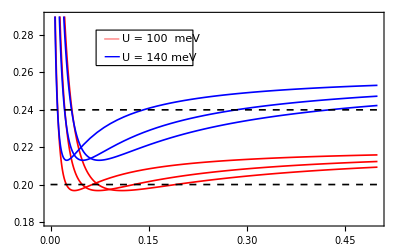

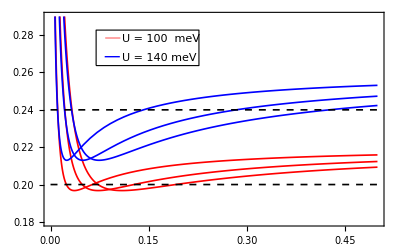

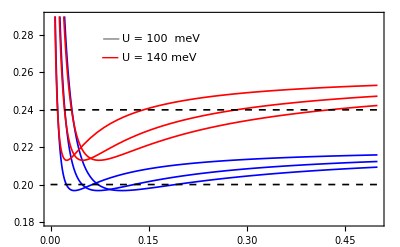

-Graphics-

```mathematica
Plot[{f6[x,1,0.12],f6[x,2,0.12],f6[x,3,0.12],f6[x,1,0.225],f6[x,2,0.225],f6[x,3,0.225],0.415,0.2},{x,0,0.5},PlotRange->{0.09,0.6},PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Red},{Thickness[0.003],Red},{Thickness[0.003],Blue},{Thickness[0.003],Blue},{Thickness[0.003],Blue},{Thickness[0.003],Dashed,Black},{Thickness[0.003],Dashed,Black}},Epilog->{{Black,Text["U = 120  meV",{0.35,0.535},{-1,-1}]},{Black,Text["U = 225 meV",{0.35,0.5},{-1,-1}]}},FrameLabel->{Style["1/B, T^-1",10],Style["E, eV",10]},Frame->True]
```